# Trabalho Individual de Fundamentos de Física 3 Lei de Coulomb

## Fundamentos de Física 3 - 2023/2 Resolução do aluno Carlos Victor de Souza Gussão Ciência da Computação Prof. Roberto Colistete Jr

## Questão 2 - 1.ba teste Lei de Coulomb Dado 2 elétrons, cada um com carga elétrica -1,60x10^-19, separados por uma distância d = 0,1nm, obtenha as forças Coulombianas entre eles, diagramando-as vetorialmente. No caso do trabalho, calcular o módulo da força F(d) para os dois elétrons, para os valores numéricos dados; Gráfico do módulo da força F(d) x d, variando d entre 0 nm e 1 nm.

```mathematica
k=1/(4×π×Subscript[ϵ, 0])=8.99 10^9

Subscript[q, 1]=-1.60  10^-19
Subscript[q, 2]=-1.60  10^-19

dist = 1×10^-10

Subscript[F, 12]=k×Abs[Subscript[q, 1]×Subscript[q, 2]]/dist^2
Subscript[F, 21]=k×Abs[Subscript[q, 2]×Subscript[q, 1]]/dist^2
Subscript[F, 12]=-Subscript[F, 21]
```

## Resultado das forças

```mathematica
Subscript[F, 21]
Subscript[F, 12]
```

2.30144×10^-8

-2.30144×10^-8

## Gráfico do módulo da força F(d) x d

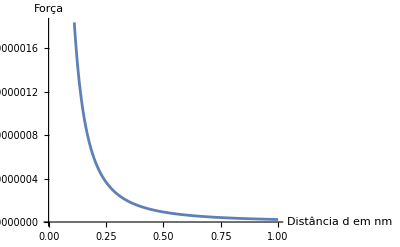

```mathematica
Plot[Abs[k*(Subscript[q, 2]×Subscript[q, 1])/d^2], {d, 0, 1*10^-10}, AxesLabel->{"Distância d em nm", "Força"}
, FrameLabel->{"Distância d em nm", "Força"}]
```